```mathematica
ClearAll["Global`*"];
```

## Waveform from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
```

```mathematica
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
```

```mathematica
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-αb[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
```

```mathematica
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[αb[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-αb[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]], αb[α1, α2]]
```

```mathematica
K[α1_, α2_, t0_, tp_]:=(OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/(1-Tanh[(t0-tp)/TAO[α1, α2]])
```

```mathematica
OM[α1_, α2_, t0_, tp_, t_]:=  (OMREF[α1, α2]^4 + K[α1, α2, t0, tp](Tanh[(t-tp)/TAO[α1, α2]] -Tanh[(t0-tp)/TAO[α1, α2]]))^(1/4)
```

```mathematica
News[α1_, α2_, t0_, tp_, t_]:= Ap[α1, α2]Sech[(t-tp)/TAO[α1, α2]]/(OM[α1, α2, t0, tp, t])
```

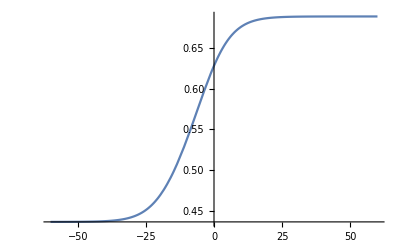

```mathematica
Plot[2(OM[0, 0, -60, 0, t]+0.15), {t, -60,60}]
```

```mathematica
Series[News[0, 0, -1, 0, t]^2, {t, 0,5}]
```

0.42418-0.181446 t+0.112416 t^2-0.0807157 t^3+0.0603249 t^4-0.0462901 t^5+O[t]^6